# PeterBurbery/LittleChildPaclet

This is a little paclet. I don't fully understand how to create a paclet yet

## Paclet Manifest

"Documentation"

"English"

"Guides"

"AssumptionsandDomains.nb"DocumentationEnglishGuidesAssumptionsandDomains.nb

"LinguisticData.nb"DocumentationEnglishGuidesLinguisticData.nb

"NumberDigits.nb"DocumentationEnglishGuidesNumberDigits.nb

"StartHereWolframChallengeFunctions.nb"DocumentationEnglishGuidesStartHereWolframChallengeFunctions.nb

"StringPatterns.nb"DocumentationEnglishGuidesStringPatterns.nb

"WolframChallengesAlgorithms.nb"DocumentationEnglishGuidesWolframChallengesAlgorithms.nb

"WolframChallengesComputationalKnowledge.nb"DocumentationEnglishGuidesWolframChallengesComputationalKnowledge.nb

"WolframChallengesWordsandLinguistics.nb"DocumentationEnglishGuidesWolframChallengesWordsandLinguistics.nb

"ReferencePages"

"Symbols"

"AliquotSequence.nb"DocumentationEnglishReferencePagesSymbolsAliquotSequence.nb

"AlmostPalindrome.nb"DocumentationEnglishReferencePagesSymbolsAlmostPalindrome.nb

"BalancedParentheses.nb"DocumentationEnglishReferencePagesSymbolsBalancedParentheses.nb

"ButterflyString.nb"DocumentationEnglishReferencePagesSymbolsButterflyString.nb

"CatalanUnrank.nb"DocumentationEnglishReferencePagesSymbolsCatalanUnrank.nb

"Coins.nb"DocumentationEnglishReferencePagesSymbolsCoins.nb

"DigitalRoot.nb"DocumentationEnglishReferencePagesSymbolsDigitalRoot.nb

"FizzBuzz.nb"DocumentationEnglishReferencePagesSymbolsFizzBuzz.nb

"IntegerPalindromeQ.nb"DocumentationEnglishReferencePagesSymbolsIntegerPalindromeQ.nb

"MaxRomanLength.nb"DocumentationEnglishReferencePagesSymbolsMaxRomanLength.nb

"MaxRomanNumeralValue.nb"DocumentationEnglishReferencePagesSymbolsMaxRomanNumeralValue.nb

"NonNegativeIntegerQ.nb"DocumentationEnglishReferencePagesSymbolsNonNegativeIntegerQ.nb

"NumberTriangle.nb"DocumentationEnglishReferencePagesSymbolsNumberTriangle.nb

"OddBeforeEven.nb"DocumentationEnglishReferencePagesSymbolsOddBeforeEven.nb

"PairsAddToHundred.nb"DocumentationEnglishReferencePagesSymbolsPairsAddToHundred.nb

"PositiveIntegerQ.nb"DocumentationEnglishReferencePagesSymbolsPositiveIntegerQ.nb

"SameStartEndWords.nb"DocumentationEnglishReferencePagesSymbolsSameStartEndWords.nb

"SayHello.nb"DocumentationEnglishReferencePagesSymbolsSayHello.nb

"SquareSum.nb"DocumentationEnglishReferencePagesSymbolsSquareSum.nb

"StringPatternQ.nb"DocumentationEnglishReferencePagesSymbolsStringPatternQ.nb

"ThreeFive.nb"DocumentationEnglishReferencePagesSymbolsThreeFive.nb

"ToMorseCode.nb"DocumentationEnglishReferencePagesSymbolsToMorseCode.nb

"TwoAndThreePointers.nb"DocumentationEnglishReferencePagesSymbolsTwoAndThreePointers.nb

"WordListLookup.nb"DocumentationEnglishReferencePagesSymbolsWordListLookup.nb

"Tutorials"

"Kernel"

"AliquotSequence.wl"KernelAliquotSequence.wl

"AlmostPalindrome.wl"KernelAlmostPalindrome.wl

"BalancedParentheses.wl"KernelBalancedParentheses.wl

"ButterflyString.wl"KernelButterflyString.wl

"CatalanUnrank.wl"KernelCatalanUnrank.wl

"Coins.wl"KernelCoins.wl

"DigitalRoot.wl"KernelDigitalRoot.wl

"FizzBuzz.wl"KernelFizzBuzz.wl

"IntegerPalindromeQ.wl"KernelIntegerPalindromeQ.wl

"LittleChildPaclet.wl"KernelLittleChildPaclet.wl

"MaxRomanLength.wl"KernelMaxRomanLength.wl

"MaxRomanNumeralValue.wl"KernelMaxRomanNumeralValue.wl

"NonNegativeIntegerQ.wl"KernelNonNegativeIntegerQ.wl

"NumberTriangle.wl"KernelNumberTriangle.wl

"OddBeforeEven.wl"KernelOddBeforeEven.wl

"PairsAddToHundred.wl"KernelPairsAddToHundred.wl

"PositiveIntegerQ.wl"KernelPositiveIntegerQ.wl

"RepeatAndEndingPrimes.wl"KernelRepeatAndEndingPrimes.wl

"SameStartEndWords.wl"KernelSameStartEndWords.wl

"SayHello.wl"KernelSayHello.wl

"SquareSum.wl"KernelSquareSum.wl

"StringPatternQ.wl"KernelStringPatternQ.wl

"ThreeFive.wl"KernelThreeFive.wl

"ToMorseCode.wl"KernelToMorseCode.wl

"TwoAndThreePointers.wl"KernelTwoAndThreePointers.wl

"WordListLookup.wl"KernelWordListLookup.wl

"PacletInfo.wl"PacletInfo.wl

"ResourceDefinition.nb"ResourceDefinition.nb

## Web Content

### Headline Image



### Basic Description

I'm creating this to get a better understanding of how to use paclets and the Paclet Repository. This will serve as a place to learn how to check, build, deploy, install, update, load, and uninstall paclets. This paclet will mainly contain simple functions that don't have a big complicated definition.

### Details

Some of the documentation examples require 13.3

### Primary Context

PeterBurbery`LittleChildPaclet`

### Main Guide Page

## Examples

### Initialization for Examples

```mathematica
PacletDirectoryLoad[NotebookDirectory[]];
```

```mathematica
Needs["PeterBurbery`LittleChildPaclet`"];
```

### Basic Examples

Write something in Morse code:

```mathematica
ToMorseCode["Morse code"]
```

-- --- .-. ... ./-.-. --- -.. .

### Scope

Say Hello World:

```mathematica
SayHello[EchoEvaluation[$Username]]
```

$Username

"Peter"

Hello Peter!

Join a string with its reversal:

```mathematica
ButterflyString["Wolfram"]
```

ButterflyString[Wolfram]

```mathematica
ButterflyString["butterfly"]
```

butterflyylfrettub

```mathematica
ButterflyString["race"]
```

raceecar

```mathematica
ButterflyString["Hello world!"]
```

Hello world!!dlrow olleH

Join a hello string with its reversal:

```mathematica
ButterflyString[EchoEvaluation[SayHello["world"]]]
```

SayHello["world"]

"Hello world!"

Hello world!!dlrow olleH

Find the maximum length of any roman numeral up to 3000:

```mathematica
MaxRomanLength[3000]
```

14

Stack successively longer lists of integers on top of each other:

```mathematica
NumberTriangle[7]
```

{1}
{1,2}
{1,2,3}
{1,2,3,4}
{1,2,3,4,5}
{1,2,3,4,5,6}
{1,2,3,4,5,6,7}

Replace multiples of 3 with fizz and multiples of 5 with buzz and multiples of 3 and 5 with fizz-buzz:

```mathematica
FizzBuzz[54]
```

{1,2,fizz,4,buzz,fizz,7,8,fizz,buzz,11,fizz,13,14,fizzbuzz,16,17,fizz,19,buzz,fizz,22,23,fizz,buzz,26,fizz,28,29,fizzbuzz,31,32,fizz,34,buzz,fizz,37,38,fizz,buzz,41,fizz,43,44,fizzbuzz,46,47,fizz,49,buzz,fizz,52,53,fizz}

Find the number of multiples of 3 and 5 up to ⌈ⅇ^12⌉:

```mathematica
ThreeFive[EchoEvaluation[⌈ⅇ^12⌉]]
```

Ceiling[ⅇ^12]

162755

10850

Find all words that begin and end with a given letter in WordList:

```mathematica
SameStartEndWords["a"]
```

{a,abracadabra,abscissa,acacia,academia,acrophobia,agenda,agoraphobia,aha,alfalfa,alga,algebra,alleluia,aloha,alpaca,alpha,alumina,alumna,ambrosia,ammonia,amnesia,amoeba,amphora,anaconda,analgesia,anaphora,anathema,anemia,anesthesia,angelica,angina,angostura,anorexia,antenna,aorta,aphasia,apnea,apologia,aqua,area,arena,aria,armada,aroma,arrhythmia,arugula,asphyxia,aspidistra,asthma,ataxia,aura,aurora,azalea}

WordListLookup is to DictionaryLookup as WordList[] is to DictionaryLookup[]:

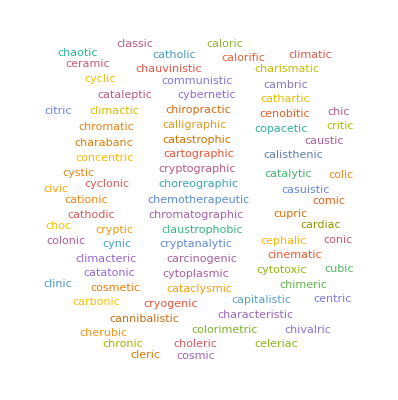

```mathematica
WordCloud[WordListLookup["c"~~___~~"c"]]
```

Test if an integer is a palindrome:

```mathematica
IntegerPalindromeQ[101]
```

True

Test if 2015 is a palindrome in base 2, binary:

```mathematica
IntegerPalindromeQ[2015,2]
```

True

Write the first sentence of the Genesis KJV in Morse code:

```mathematica
GenesisKJV=ContentObject[ExampleData[{"Text","GenesisKJV"}]]
```

ContentObject[…]

```mathematica
Thread[ToMorseCode[TextSentences[GenesisKJV,1]]]//InputForm
```

{"1 : 1/.. -./- .... ./-... . --. .. -. -. .. -. --./--. --- \
-../-.-. .-. . .- - . -../- .... ./.... . .- ...- . -./.- -. \
-../- .... ./. .- .-. - ...."}

Iteratively sum and square all integers from 1 to 10:

```mathematica
SquareSum[10]
```

63073033198182852557686460280588385280848487006086558259464092063436128175134417077664303895453873373039212220029711960864138033087202698165344048976623585078720506691737183512319543297562843619936727988132209328160703301424563585824706897928104440032778766396489516930962875225

Test if input is a positive integer:

```mathematica
PositiveIntegerQ[1]
```

True

```mathematica
PositiveIntegerQ[0]
```

False

```mathematica
PositiveIntegerQ[-1]
```

False

Find all ways to score 21 points with two pointers and three pointers in basketball:

```mathematica
TwoAndThreePointers[21]
```

{{3,3,3,3,3,3,3},{2,2,2,3,3,3,3,3},{2,2,2,2,2,2,3,3,3},{2,2,2,2,2,2,2,2,2,3}}

Rearrange a list of integers so all odd integers appear before all even integers, without changing the order otherwise:

```mathematica
OddBeforeEven[EchoEvaluation[Array[Fibonacci,20]]]
```

Array[Fibonacci,20]

{1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765}

{1,1,3,5,13,21,55,89,233,377,987,1597,4181,6765,2,8,34,144,610,2584}

Find all distinct pairs that sum to 100 in a list of integers:

```mathematica
PairsAddToHundred[{34,-65,-40,12,174,44,-186,169,-136,153,-15,127,29,15,-87,191,102,-3,26,-175,36,21,177,-135,-77,138,166,-140,-187,156,-88,100,183,-81,-68,-18,120,37,-167,-104,-145,-59,160,-105,-53,-120,70,-46,172,22,56,-134,-8,-174,-57,39,84,-50,19,-106,-133,-161,-169,171,108,-45,122,-55,61,25,24,14,-17,135,114,188,-14,-7,-25,-61,69,52,-72,-125,20,149,-132,199,-13,-170,157,-4,-38,168,89,-124,85,8,189,196}]
```

{{85,15},{168,-68},{-38,138},{157,-57},{-72,172},{-14,114},{188,-88},{61,39},{108,-8},{56,44},{-53,153},{-77,177}}

Find the digital root of 1234:

```mathematica
DigitalRoot[1234]
```

1

## Source & Additional Information

### Creator

Peter Burbery

### Source Control Repository

https://github.com/UserName/MyPaclet

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

keyword 1

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Original Source References and Attributions

Source, reference or citation

### Links

Link to other related material

### Compatibility

#### Wolfram Language Version

13.2+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

### Disclosures

Local filesDisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more information

Wolfram accountDisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more information

External servicesDisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more information

Wolfram Language system configurationDisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies $Path, Directory, or similar
◼ Installs additional paclets or dependencies
◼ Creates or imports non-public ResourceObject content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more information

Wolfram Language built-in symbolsDisclosuresWLSystemSymbolsChoose this option if your paclet directly modifies definitions of built-in symbols such as those in System` or other internal contexts.Click for more information

Paclet dependenciesDisclosuresPacletDependenciesChoose this option if your paclet directly installs or updates any additional paclets. Paclets that are included with the Wolfram system do not require a disclosure.Click for more information

OS configurationDisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of SystemCredentialClick for more information

Local system interactionsDisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via ExternalEvaluate
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more information

OtherDisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more information

## Author Notes

Additional information about limitations, issues, etc.

CodeInspector`SuppressedRegions`SuppressedRegions::missingpop: -- Message text not found --